```mathematica
pi=SetPrecision[3.141592,8];
```

```mathematica
x0={0,pi/6,pi/4,pi/3,pi/2}
f0={0,Sin[2pi/6],Sin[2pi/4],Sin[2pi/3],Sin[2pi/2]}
L=Length[x0]
p={pi/12,5pi/12,7pi/24}
```

{0,0.52359867,0.785398,1.0471973,1.570796}

{0,0.86602529,0.99999999999995,0.8660256,7.×10^-7}

5

{0.26179933,1.3089967,0.91629767}

```mathematica
A[k_]:=1/Product[x0[[k]]-x0[[i]],{i,Complement[Range[L],{k}]}]

P[x_]:=Sum[(A[i] f0[[i]])/(x-x0[[i]]),{i,L}]/Sum[A[i]/(x-x0[[i]]),{i,L}]
```

```mathematica
P/@p
```

{0.4984,0.4984,0.965971}

```mathematica
Sin/@ (2p)
```

{0.49999991,0.5000005,0.96592592}

```mathematica
Abs[Sin/@ (2p)-P/@p]
```

{0.0016,0.0016,0.00004}

```mathematica
Clear[LP]

LP[1,i_,x_]:=1/(x0[[i+1]]-x0[[i]])Det[({{f0[[i]], x0[[i]]-x}, {f0[[i+1]], x0[[i+1]]-x}})]
```

```mathematica
LP[1,1,1]
```

1.653987

```mathematica
LP[n_,i_,x_]:=1/(x0[[i+n]]-x0[[i]])Det[({{LP[n-1,i,x], x0[[i]]-x}, {LP[n-1,i+1,x], x0[[i+n]]-x}})]
```

```mathematica
LP[4,1,7pi/24]
```

1.

```mathematica
Precision[0.96597058630768173854270730610157030912`1.3181544851082272]
```

1.31815

```mathematica
LP[4,1,x]
```

0.6366199 (3.074 x+0.401 x^2-3.002 x^3+0.9556 x^4)

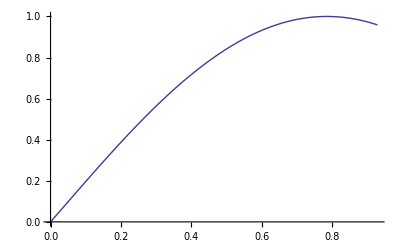

```mathematica
Plot[%101,{x,0,7.1pi/24}]
```

```mathematica
P[x]
```

((1.×10^-6)/(-1.570796+x)-11.5222/(-1.0471973+x)+23.6528/(-0.785398+x)-11.5222/(-0.52359867+x))/(1.4783/(-1.570796+x)-13.3047/(-1.0471973+x)+23.6528/(-0.785398+x)-13.3047/(-0.52359867+x)+1.478303/x)

```mathematica
Simplify[%107]
```

0.003 x (-1.+4. x-3. x^2+1. x^3)

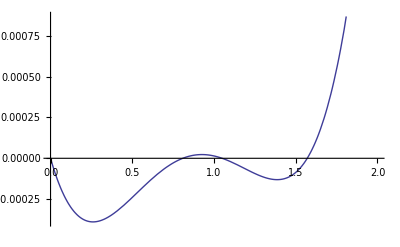

```mathematica
Plot[%108,{x,0,2}]
```